```mathematica
dataGet[str_String,page_]:=Table[Block[{url},url="https://scholar.google.co.uk/scholar?start="<>URLEncode[i]<>"&q="<>URLEncode[str]<>"&hl=en&as_sdt=0,5";
Cases[Cases[Import[url,"XMLObject"],XMLElement["div",{"id"->"gs_ccl","role"->"main"},___],Infinity],XMLElement["h3",{"class"->"gs_rt"},___],Infinity]],{i,1,page}]
parseData2[dataIn_]:=ToLowerCase@DeleteStopwords@Flatten@TextWords@Table[DeleteCases[Cases[dataRaw,XMLElement["a",_,_],Infinity][[i]],XMLElement["b",_,_],Infinity][[3]],{i,1,Length@dataRaw[[1]]*Length@dataRaw}]
parseData1[dataIn_]:=DeleteStopwords@Flatten@TextWords@Table[Cases[dataIn,XMLElement["a",_,_],Infinity][[i]][[3]][[1]],{i,1,Length@dataRaw[[1]]*Length@dataRaw}]
associate[words_]:=Flatten[Map[(Thread[#->DeleteCases[Nearest[words,#,3],#]])&,words]];

commonAssociateMinus[dataParsed_,Ncommonest_,minusWords_]:=associate[DeleteCases[Commonest[dataParsed,Ncommonest],minusWords]]
```

```mathematica
url="https://www.google.de/search?ei=Ulv7We3yA4G1adfFvuAI&btnG=Search&q=%22ultra-high+temperature+ceramics%22";
```

```mathematica
urlin=Import[url];
```

$CharacterEncoding::utf8: The byte sequence {176} could not be interpreted as a character in the UTF-8 character encoding.

General::stop: Further output of $CharacterEncoding::utf8 will be suppressed during this calculation.

```mathematica
data1="Scholarly articles for \"ultra-high temperature ceramics\"
Evaluation of ultra-high temperature ceramics … - ‎Levine - Cited by 583
… /silicon carbide ultra high temperature ceramics - ‎Gasch - Cited by 278
… 2-and HfB 2-based ultra-high temperature ceramics: … - ‎Opila - Cited by 211
Search Results
Ultra-high-temperature ceramics - Wikipedia
https://en.wikipedia.org/wiki/Ultra-high-temperature_ceramics
Ultra-high-temperature ceramics (UHTCs) are a class of refractory ceramics that offer excellent stability at temperatures exceeding 2000 °C being investigated ...
‎History · ‎Physical properties · ‎Structure · ‎Synthesis of diboride (Zr ...
Ultra-High Temperature Ceramics - An Introduction to Ultra-High ...
https://www.azom.com/article.aspx?ArticleID=5127
21 Feb 2010 - Ultra-high temperature ceramics (UHTCs) are a class of materials that can be used in environments that exhibit extremes in temperature, ...
[PDF]Ultra-High Temperature Ceramic Materials for Extreme Environment
https://www.electrochem.org/dl/interface/wtr/wtr07/wtr07_p30-36.pdf
by E Wuchina - ‎2007 - ‎Cited by 244 - ‎Related articles
Ultra-High Temperature Ceramics are a family of compounds that display a unique set of properties, including extremely high melting temperatures. (> 3000°C) ...
Technology Opportunity: Ultra High Temperature Ceramics (UHTC ...
https://www.nasa.gov/ames-partnerships/technology/ultra-high-temperature-ceramics
Ultra high temperature ceramics (UHTC), composed primarily of metal diborides, are candidate materials for sharp leading edges on hypersonic re-entry ...
[PDF]The Next Steps for Ultra-High Temperature Ceramics
dc.engconfintl.org/cgi/viewcontent.cgi?article=1001&context=uhtc
by E Wuchina - ‎2014
14 May 2014 - Ultra-High Temperature Ceramics: Materials For Extreme Environmental Applications II by an authorized administrator of ECI Digital Archives.
[PDF]Ultra-High-Temperature Ceramics - ASM International
www.asminternational.org/documents/.../74f528fa-22ed-4b1c-98d0-07e05f3a388a
Ultra-high temperature ceramics (UHTCs) are defined as ceramic materials with melting points higher than 2500°C. The interest in them began in the 1960s.
Ultra-high temperature ceramics: Materials for extreme environments
www.sciencedirect.com/science/article/pii/S1359646216305139
by WG Fahrenholtz - ‎2017 - ‎Cited by 15 - ‎Related articles
This paper identifies gaps in the present state of knowledge and describes emerging research directions for ultra-high temperature ceramics. Borides, carbides,
[PDF]Ultra High Temperature Ceramics - The American Ceramic Society
ceramics.org/wp-content/uploads/2011/08/applicatons-uhtc-johnson.pdf
3 Aug 2011 - Ultra High Temperature Ceramics. (UHTCs) : A Family of Materials. • Borides, carbides and nitrides of transition elements such as hafnium, ...
Materials | Special Issue : Ultra-high Temperature Ceramics - MDPI
www.mdpi.com/journal/materials/special_issues/temperature-ceramics
Borides, carbides, and nitrides of the transition metals comprise a family of ultra-refractory materials known as ultra-high-temperature ceramics (UHTCs), and are ...
Wiley: Ultra-High Temperature Ceramics: Materials for Extreme ...
www.wiley.com › ... › Engineering & Materials Science › Materials Science › Ceramics
The first comprehensive book to focus on ultra-high temperature ceramic materials in more than 20 years. Ultra-High Temperature Ceramics are a family of ...
Ad
High- Temperature Ceramic‎
Adwww.vitcas.com/High-+Temperature+Ceramic‎0117 911 7895
Manufacturer of Heat Resistant High Quality Adhesives, Cements
Competitive Prices · High Quality Products · High Quality Materials · In Business Since 1882
Products: Heat Resistant Plaster, Fire Bricks, Fire Cement";
data2="Ultra-High Temperature Ceramics: Materials for Extreme Environment ...
www.engconf.org/ultra-high-temperature-ceramics-materials-for-extreme-environme...
Ultra-High Temperature Ceramics are a family of compounds that display a unique set of properties, including extremely high melting temperatures (>3000°C), ...
New ceramic coating could have hypersonic applications - The Engineer
https://www.theengineer.co.uk/new-ceramic-coating-could-have-hypersonic-applicati...
10 Jul 2017 - Amongst other materials, current spacecraft and missiles rely on ultra-high temperature ceramics (UHTCs) to combat high temperatures.
Ultra-High Temperature Ceramics: Materials for Extreme ... - Amazon UK
https://www.amazon.co.uk/Ultra-High-Temperature-Ceramics.../dp/1118700783
Buy Ultra-High Temperature Ceramics: Materials for Extreme Environment Applications 1 by William G. Fahrenholtz, Eric J. Wuchina, William E. Lee, Yanchun ...
Ultra-High Temperature Ceramics: Materials for ... - Wiley Online Library
onlinelibrary.wiley.com › Materials Science › Ceramics
by WG Fahrenholtz - ‎Cited by 48 - ‎Related articles
10 Oct 2014 - Ultra-High Temperature Ceramics are a family of compounds that display an unusual combination of properties, including extremely high ...
[PDF]Ultra High Temperature Ceramics for Hypersonic Vehicle Applications
prod.sandia.gov/techlib/access-control.cgi/2006/062925.pdf
by R Loehman - ‎Cited by 119 - ‎Related articles
Ultra High Temperature Ceramics for. Hypersonic Vehicle Applications. Ronald Loehman, Erica Corral, Hans Peter Dumm, Paul Kotula, and Rajan Tandon.
Ultra High Temperature Ceramics: Densification, Properties and ...
www.aerospacelab-journal.org/al3/Ultra-High-Temperature-Ceramics
Ultra High Temperature Ceramics (UHTCs) are good candidates tofulfill these requirements. Within this family, the ZrB2 and HfB2 based composites are the ...
Theory and simulation of ultra-high-temperature ceramics
www3.imperial.ac.uk/portal/page/.../5C847B22E2C0B7AAE050C69B473946F3
6 Nov 2017 - Ultra-high-temperature ceramics are a class of refractory materials with remarkable properties. High melting-points (TC > 3000 K) are ...
Images for \"ultra-high temperature ceramics\"
Image result for \"ultra-high temperature ceramics\"
Image result for \"ultra-high temperature ceramics\"
Image result for \"ultra-high temperature ceramics\"
Image result for \"ultra-high temperature ceramics\"
Image result for \"ultra-high temperature ceramics\"
More images for \"ultra-high temperature ceramics\"
Report images
Amazing Technology - Ultra-High Temperature Ceramics - YouTube
Video for \"ultra-high temperature ceramics\"▶ 3:07
https://www.youtube.com/watch?v=Er22T8Pe6ag
15 May 2014 - Uploaded by Public Domain TV
A key to building denser, stronger materials that won't fail or fracture under extreme conditions is the ...
Next Generation: Ultra-high temperature ceramics - YouTube
Video for \"ultra-high temperature ceramics\"▶ 2:14
https://www.youtube.com/watch?v=A-pd3ia8Y4g
13 May 2010 - Uploaded by tucsonbusiness
University of Arizona Associate Professor Erica Corral, PhD, explains how the Arizona Materials Lab uses its ...
Ads
Ultra High Temperature Ceramics - Mingrui Ceramic Factory‎
Adwww.machiningceramicparts.com/ceramic_parts/ceramic_sheet‎
Refractory Alumina and Ziroconia Ceramic Sheet, Ceramic Grooved Blocks.
safe payment · fast delivery · factory direct · quality assurance
ceramic locating blockalumina ceramic block
High Temperature Materials - High Temperate Epoxy Adhesive Materials‎
Adwww.cotronics.com/‎
For Use Up To 4000.baF!";
data3="Ultra High Temperature Ceramics Highly Pure Lowest Price - Nanoshel
https://www.nanoshel.com/sections/ultra-high-temperature-ceramics/
We Provide Ultra High Temperature Ceramics high quality Worldwide Shipping From us You can easily purchase Ultra High Temperature Ceramics at great price.
Effective thermal conductivity of ultra-high temperature ceramics with ...
iopscience.iop.org/article/10.1088/0031-8949/86/05/055402
by W Li - ‎2012 - ‎Cited by 2 - ‎Related articles
The new model is applied to the effective thermal conductivity of ultra-high temperature ceramics. The predictions agree well with the experimental data.
MSE Professor Erica Corral's Engineering Lab Gets Ultra High ...
mse.arizona.edu/mse-professor-erica-corrals-engineering-lab-gets-ultra-high-temperat...
MSE Professor Erica Corral's Engineering Lab Gets Ultra High-Temperature Ceramics Oven. April 2013 - The UA's Erica Corral and her team create and test ...
Ultra High Temperature Ceramics for Aerospace Applications
https://benthamopen.com/TOAEJ/VOLUME/3/ISSUE/001/
Arc-Jet Testing of Ultra-High-Temperature-Ceramics · The Open Aerospace Engineering Journal , 2010, 3: 20-31. Raffaele Savino, Mario De Stefano Fumo, ...
Toward Oxidation-Resistant ZrB2-SiC Ultra High Temperature Ceramics
https://link.springer.com/article/10.1007/s11661-010-0540-8
by E Eakins - ‎2011 - ‎Cited by 73 - ‎Related articles
23 Nov 2010 - Ultra high temperature ceramics (UHTCs), including ZrB2-SiC, are designed for extreme environment applications in which temperatures ...
Plasma Torch Test of an Ultra-High-Temperature Ceramics Nose ...
https://arc.aiaa.org/doi/abs/10.2514/1.42834
by L Scatteia - ‎2010 - ‎Cited by 11 - ‎Related articles
Luigi Scatteia, Davide Alfano, Stefania Cantoni, Frederic Monteverde, Andrea Di Maso, and M. De Stefano Fumo. \"Plasma Torch Test of an ...
Topical Issue on Ultra-High-Temperature Ceramics | SRI International
https://www.sri.com/work/publications/topical-issue-ultra-high-temperature-ceramics
Topical Issue on Ultra-High-Temperature Ceramics. May, 2008. Journal Name: Journal of the American Ceramic Society. 91. Number: 5. Yigal Blum. Journal.
ECerS - Ultra-High temperature Ceramics
ecers.org/en/ultra-high-temperature-ceramics.html?cmp_id=7&news_id=93
Ultra-high temperature ceramics (UHTCs), including transition metal diborides and carbides, are characterized by melting temperatures exceeding 3000°C and ...
Ultra-High Temperature Ceramic (UHTC) Composites at University of ...
https://www.findaphd.com/search/projectdetails.aspx?PJID=81394
University of Edinburgh School of Engineering · Modelling and simulation of degradation of ultra high temperature ceramics (UHTCs) under hypersonic flow.
Design of Ultra-High Temperature Ceramics for Improved Performance
www.dtic.mil/docs/citations/ADA495056
by WG Fahrenholtz - ‎2009 - ‎Cited by 2 - ‎Related articles
The thermal shock behavior and thermal residual stresses were investigated for zirconium diboride-based ultra-high temperature ceramics. The research ...";
data4="Design of Ultra-High Temperature Ceramics for Improved Performance
www.dtic.mil/docs/citations/ADA495056
by WG Fahrenholtz - ‎2009 - ‎Cited by 2 - ‎Related articles
The thermal shock behavior and thermal residual stresses were investigated for zirconium diboride-based ultra-high temperature ceramics. The research ...
[PDF]Ultra High Temperature Ceramics for aerospace applications - Hal
https://hal.archives-ouvertes.fr/hal-01103216v1/document
14 Jan 2015 - Ultra High Temperature Ceramics for aerospace applications. A. Jankowiak, J.F. Justin. To cite this version: A. Jankowiak, J.F. Justin. Ultra High ...
Fracture mechanisms of zirconium diboride ultra-high temperature ...
aip.scitation.org/doi/abs/10.1063/1.4971628
by VV Skripnyak - ‎2017 - ‎Related articles
Fracture mechanisms of zirconium diboride ultra-high temperature ceramics under pulse loading. Vladimir V. Skripnyak 1, a), Anatoly M. Bragov 2, b), Vladimir A.
Ultra-High Temperature Ceramics | Global Events |USA| Europe ...
https://www.omicsonline.org/conferences-list/ultra-high-temperature-ceramics
Ultra-High Temperature Ceramics are a family of compounds that display a unique set of properties, including extremely high melting temperatures (>3000°C), ...
temperature and microstructures dependent thermal shock resistance ...
https://www.cambridge.org/.../div-class-title-temperature-and-microstructures-dependent...
by RZ Wang - ‎2013 - ‎Cited by 1 - ‎Related articles
thermal shock resistance can be achieved through our studies. Keywords: Ultra-high-temperature ceramics, Residual stress, Microstructures, Thermal shock re-.
Ultra-High Temperature Ceramics | Global Events | USA| Europe ...
https://ceramics.conferenceseries.com/events-list/ultra-high-temperature-ceramics
Ultra-High Temperature Ceramics are a family of compounds that display a unique set of properties, including extremely high melting temperatures (>3000°C), ...
Efficient Technologies for the Fabrication of Dense TaB2-Based Ultra ...
pubs.acs.org/doi/abs/10.1021/am100211h
by R Licheri - ‎2010 - ‎Cited by 19 - ‎Related articles
21 Jun 2010 - Efficient Technologies for the Fabrication of Dense TaB2-Based Ultra-High-Temperature Ceramics. Roberta Licheri, Roberto Orrù*, Clara Musa ...
Turning up the heat: Laser ablation of ultra-high temperature ceramics
www.twi-global.com/.../turning-up-the-heat-laser-ablation-of-ultra-high-temperature-...
Ultra-high temperature ceramics (UHTCs), for example, have been identified as having an important role to play in nuclear power generation and radioactive ...
Ultra high temperature ceramics for space and industrial applications
www.istec.cnr.it › Home › Research Areas
Transition metals (Ti, Zr, Hf, Ta) form borides and carbides that belong to a class of advanced materials defined as Ultra High Temperature Ceramics (UHTCs) ...
ultra high temperature ceramics - Tag | PBS NewsHour
https://www.pbs.org/newshour/tag/ultra-high-temperature-ceramics
Nation Oct 22. Incarcerated women risk their lives fighting California fires. It's part of a long history of prison labor. By Kamala Kelkar. Health Oct 22.";
```

```mathematica
urlin;
```

```mathematica
deleteWords={"PDF","PDF]Book","Ebook","III","5","1","2","3","4","6","7","8","9","E","10","PDF]Annual","ebook","download","Archives","","O","75b99af8516df502b589cb61fed241ea","7"‎,"Related","ePub","Mobi","Jan","operate","21","Apr","cpas","Nlr","area","year","completely","Related","sites","Onera","1stFebruary","Related","started","ceramics","Ultra-high-temperature","ultra-high","ultra-high-temperature","2010","Wiley","2009","www.dtic.mil/docs/citations/ADA495056","M","Scatteia","De","Stefano","Fumo","Journal","MSE","Corral's","Gets","ceramics\"▶","Uploaded","University","Arizona","Professor","Lab","PDF]Ultra","15","WG","defined","2014","14","display","set",",","‎Cited","2010","2011","quality","2013","articles","Cited","class","‎Cited","‎Related","Wuchina","William","583","278","2-based","2-","‎Opila","211","Search","Results","Wikipedia","https://en.wikipedia.org/wiki/Ultra-high-temperature_ceramics","https://www.azom.com/article.aspx?ArticleID=5127","https://www.nasa.gov/ames-partnerships/technology/ultra-high-temperature-ceramics","Scholarly","Evaluation","‎Levine","‎Gasch","offer","excellent","exceeding","investigated","‎History",,"‎Synthesis","diboride","Zr",,"Introduction","Feb","used","environments","exhibit","PDF]Ultra-High","https://www.electrochem.org/dl/interface/wtr/wtr07/wtr07_p30-36.pdf","‎","2007","244","family","compounds","unique","including","extremely","Opportunity","composed","primarily","candidate","PDF]","Steps","dc.engconfintl.org/cgi/viewcontent.cgi?article=1001&context=uhtc","Environmental","II","authorized","administrator","ECI","Digital","PDF]Ultra-High-Temperature","ASM","International","www.asminternational.org/documents/.../74f528fa-22ed-4b1c-98d0-07e05f3a388a","points","began","1960s","www.sciencedirect.com/science/article/pii/S1359646216305139","Fahrenholtz","2017","paper","identifies","American","Issue","Quality","Products","applications","Oct","R","Loehman","Erica","Corral","Nov","Image","result","images","YouTube","Video","Test","Topical","Improved","behavior","residual","Jankowiak","J.F.","Justin","Skripnyak","Vladimir","Events","Technologies","Licheri","22","°C","properties","Applications","Global","research","Technology","2000","Science","temperatures","higher","Aug","Special","MDPI","www.mdpi.com/journal/materials/special_issues/temperature-ceramics","Family","gaps","present","state","knowledge","describes","emerging","directions","Society","ceramics.org/wp-content/uploads/2011/08/applicatons-uhtc-johnson.pdf","www.wiley.com","Torch","comprehensive"};
extraWords=Join[{Table["ZrC",5],Table["Finnis",2],Table["Binner",3],Table["Imperial",5],Table["NASA",5],Table["ultra",8],Table["nuclear",8]}];
wordData=Commonest[DeleteStopwords@Flatten@TextWords@Join@{DeleteCases[Join@{Table[data1,1],Table[data2,1],Table[data3,1],Table[data4,1]},"PDF]Book"],extraWords},250];
wordData2=DeleteStopwords@Flatten@TextWords@Join@{DeleteCases[Join@{Table[data1,1],Table[data2,1],Table[data3,1],Table[data4,1]},"PDF]Book"],extraWords};
cloudData=Module[{loopData=wordData},For[i=1,i<Length[deleteWords]+1,i++,loopData=DeleteCases[loopData,deleteWords[[i]]]];loopData]
cloudData2=Module[{loopData=wordData2},For[i=1,i<Length[deleteWords]+1,i++,loopData=DeleteCases[loopData,deleteWords[[i]]]];loopData]
```

{temperature,silicon,carbide,ultra,high,HfB,UHTCs,refractory,stability,‎Physical,‎Structure,Ultra-High,Temperature,Ceramics,Ultra-high,materials,extremes,Ceramic,Materials,Extreme,Environment,melting,3000°C,Ultra,High,UHTC,metal,diborides,sharp,leading,edges,hypersonic,re-entry,ceramic,2500°C,extreme,Borides,carbides,nitrides,transition,elements,hafnium,metals,comprise,ultra-refractory,known,Engineering,Heat,Resistant,Fire,Hypersonic,Vehicle,simulation,thermal,conductivity,Aerospace,ZrB2-SiC,Plasma,Ultra-High-Temperature,Design,Performance,shock,stresses,zirconium,diboride-based,aerospace,Fracture,mechanisms,USA,Europe,resistance,Efficient,Fabrication,Dense,TaB2-Based,nuclear,ZrC,Finnis,Binner,Imperial,NASA}

{temperature,temperature,silicon,carbide,ultra,high,temperature,HfB,temperature,UHTCs,refractory,stability,‎Physical,‎Structure,Ultra-High,Temperature,Ceramics,Ultra-High,Ultra-high,temperature,UHTCs,materials,extremes,temperature,Temperature,Ceramic,Materials,Extreme,Environment,Ultra-High,Temperature,Ceramics,high,melting,3000°C,Ultra,High,Temperature,Ceramics,UHTC,Ultra,high,temperature,UHTC,metal,diborides,materials,sharp,leading,edges,hypersonic,re-entry,Ultra-High,Temperature,Ceramics,Ultra-High,Temperature,Ceramics,Materials,Extreme,Ceramics,Ultra-high,temperature,UHTCs,ceramic,materials,melting,2500°C,Ultra-high,temperature,Materials,extreme,temperature,Borides,carbides,High,Temperature,Ceramics,Ceramic,Ultra,High,Temperature,Ceramics,UHTCs,Materials,Borides,carbides,nitrides,transition,elements,hafnium,Materials,Ultra-high,Temperature,Ceramics,Borides,carbides,nitrides,transition,metals,comprise,ultra-refractory,materials,known,UHTCs,Ultra-High,Temperature,Ceramics,Materials,Extreme,Engineering,Materials,Materials,Ceramics,book,focus,temperature,ceramic,materials,20,years,Ultra-High,Temperature,Ceramics,Ad,High,Temperature,Ceramic‎,Adwww.vitcas.com/High-+Temperature+Ceramic‎0117,911,7895,Manufacturer,Heat,Resistant,High,Adhesives,Cements,Competitive,Prices,High,High,Materials,Business,1882,Heat,Resistant,Plaster,Fire,Bricks,Fire,Cement,Ultra-High,Temperature,Ceramics,Materials,Extreme,Environment,www.engconf.org/ultra-high-temperature-ceramics-materials--extreme-environme,Ultra-High,Temperature,Ceramics,high,melting,3000°C,New,ceramic,coating,hypersonic,Engineer,https://www.theengineer.co.uk/new-ceramic-coating---hypersonic-applicati,Jul,Amongst,materials,current,spacecraft,missiles,rely,temperature,UHTCs,combat,high,Ultra-High,Temperature,Ceramics,Materials,Extreme,Amazon,UK,https://www.amazon.co.uk/Ultra-High-Temperature-Ceramics.../dp/1118700783,Buy,Ultra-High,Temperature,Ceramics,Materials,Extreme,Environment,G,Eric,J,E.,Lee,Yanchun,Ultra-High,Temperature,Ceramics,Materials,Online,Library,onlinelibrary.wiley.com,Materials,Ceramics,48,Ultra-High,Temperature,Ceramics,unusual,combination,high,High,Temperature,Ceramics,Hypersonic,Vehicle,prod.sandia.gov/techlib/access-control.cgi/2006/062925.pdf,119,Ultra,High,Temperature,Ceramics,Hypersonic,Vehicle,Ronald,Hans,Peter,Dumm,Paul,Kotula,Rajan,Tandon,Ultra,High,Temperature,Ceramics,Densification,Properties,www.aerospacelab-journal.org/al3/Ultra-High-Temperature-Ceramics,Ultra,High,Temperature,Ceramics,UHTCs,good,candidates,tofulfill,requirements,ZrB2,HfB2,based,composites,Theory,simulation,www3.imperial.ac.uk/portal/page/.../5C847B22E2C0B7AAE050C69B473946F3,refractory,materials,remarkable,High,melting-points,TC,3000,K,Images,temperature,temperature,temperature,temperature,temperature,temperature,temperature,Report,Amazing,Ultra-High,Temperature,Ceramics,temperature,3:07,https://www.youtube.com/watch?v=Er22T8Pe6ag,Public,Domain,TV,key,building,denser,stronger,materials,fail,fracture,extreme,conditions,Generation,Ultra-high,temperature,temperature,2:14,https://www.youtube.com/watch?v=-pd3ia8Y4g,13,tucsonbusiness,Associate,PhD,explains,Materials,uses,Ads,Ultra,High,Temperature,Ceramics,Mingrui,Ceramic,Factory‎,Adwww.machiningceramicparts.com/ceramic_parts/ceramic_sheet‎,Refractory,Alumina,Ziroconia,Ceramic,Sheet,Ceramic,Grooved,Blocks,safe,payment,fast,delivery,factory,direct,assurance,ceramic,locating,blockalumina,ceramic,block,High,Temperature,Materials,High,Temperate,Epoxy,Adhesive,Materials‎,Adwww.cotronics.com/‎,Use,4000.baF,Ultra,High,Temperature,Ceramics,Highly,Pure,Lowest,Price,Nanoshel,https://www.nanoshel.com/sections/ultra-high-temperature-ceramics,Provide,Ultra,High,Temperature,Ceramics,high,Worldwide,Shipping,easily,purchase,Ultra,High,Temperature,Ceramics,great,price,Effective,thermal,conductivity,temperature,iopscience.iop.org/article/10.1088/0031-8949/86/05/055402,W,Li,2012,new,model,applied,effective,thermal,conductivity,temperature,predictions,agree,experimental,data,Engineering,Ultra,High,mse.arizona.edu/mse-professor-erica-corrals-engineering-lab-gets-ultra-high-temperat,Engineering,Ultra,High-Temperature,Ceramics,Oven,April,UA's,team,create,test,Ultra,High,Temperature,Ceramics,Aerospace,https://benthamopen.com/TOAEJ/VOLUME/3/ISSUE/001,Arc-Jet,Testing,Ultra-High-Temperature-Ceramics,Open,Aerospace,Engineering,20-31,Raffaele,Savino,Mario,Oxidation-Resistant,ZrB2-SiC,Ultra,High,Temperature,Ceramics,https://link.springer.com/article/10.1007/s11661-010-0540-8,Eakins,73,23,Ultra,high,temperature,UHTCs,ZrB2-SiC,designed,extreme,environment,Plasma,Ultra-High-Temperature,Ceramics,Nose,https://arc.aiaa.org/doi/abs/10.2514/1.42834,L,11,Luigi,Davide,Alfano,Stefania,Cantoni,Frederic,Monteverde,Andrea,Di,Maso,Plasma,Ultra-High-Temperature,Ceramics,SRI,https://www.sri.com/work/publications/topical-issue-ultra-high-temperature-ceramics,Ultra-High-Temperature,Ceramics,2008,Name,Ceramic,91,Number,Yigal,Blum,ECerS,Ultra-High,temperature,Ceramics,ecers.org/en/ultra-high-temperature-ceramics.html?cmp_id=7&news_id=93,Ultra-high,temperature,UHTCs,transition,metal,diborides,carbides,characterized,melting,3000°C,Ultra-High,Temperature,Ceramic,UHTC,Composites,https://www.findaphd.com/search/projectdetails.aspx?PJID=81394,Edinburgh,School,Engineering,Modelling,simulation,degradation,ultra,high,temperature,UHTCs,hypersonic,flow,Design,Ultra-High,Temperature,Ceramics,Performance,thermal,shock,thermal,stresses,zirconium,diboride-based,temperature,Design,Ultra-High,Temperature,Ceramics,Performance,thermal,shock,thermal,stresses,zirconium,diboride-based,temperature,High,Temperature,Ceramics,aerospace,Hal,https://hal.archives-ouvertes.fr/hal-01103216v1/document,2015,Ultra,High,Temperature,Ceramics,aerospace,cite,version,Ultra,High,Fracture,mechanisms,zirconium,temperature,aip.scitation.org/doi/abs/10.1063/1.4971628,VV,Fracture,mechanisms,zirconium,temperature,pulse,loading,V,Anatoly,Bragov,b,Ultra-High,Temperature,Ceramics,USA,Europe,https://www.omicsonline.org/conferences-list/ultra-high-temperature-ceramics,Ultra-High,Temperature,Ceramics,high,melting,3000°C,temperature,microstructures,dependent,thermal,shock,resistance,https://www.cambridge.org/.../div-class-title-temperature--microstructures-dependent,RZ,Wang,thermal,shock,resistance,achieved,studies,Keywords,Residual,stress,Microstructures,Thermal,shock,re,Ultra-High,Temperature,Ceramics,USA,Europe,https://ceramics.conferenceseries.com/events-list/ultra-high-temperature-ceramics,Ultra-High,Temperature,Ceramics,high,melting,3000°C,Efficient,Fabrication,Dense,TaB2-Based,Ultra,pubs.acs.org/doi/abs/10.1021/am100211h,19,Jun,Efficient,Fabrication,Dense,TaB2-Based,Ultra-High-Temperature,Ceramics,Roberta,Roberto,Orrù,Clara,Musa,Turning,heat,Laser,ablation,temperature,www.twi-global.com/.../turning---heat-laser-ablation--ultra-high-temperature,Ultra-high,temperature,UHTCs,example,identified,important,role,play,nuclear,power,generation,radioactive,Ultra,high,temperature,space,industrial,www.istec.cnr.,Home,Research,Areas,Transition,metals,Ti,Hf,Ta,form,borides,carbides,belong,advanced,materials,Ultra,High,Temperature,Ceramics,UHTCs,ultra,high,temperature,Tag,PBS,NewsHour,https://www.pbs.org/newshour/tag/ultra-high-temperature-ceramics,Nation,Incarcerated,women,risk,lives,fighting,California,fires,long,history,prison,labor,Kamala,Kelkar,Health,ZrC,ZrC,ZrC,ZrC,ZrC,Finnis,Finnis,Binner,Binner,Binner,Imperial,Imperial,Imperial,Imperial,Imperial,NASA,NASA,NASA,NASA,NASA,ultra,ultra,ultra,ultra,ultra,ultra,ultra,ultra,nuclear,nuclear,nuclear,nuclear,nuclear,nuclear,nuclear,nuclear}

```mathematica
Tally[cloudData2];
```

```mathematica
data10=Join[{{"temperature",31},{"silicon",1},{"carbide",4},{"ultra",11},{"high",13},{"HfB",1},{"UHTCs",12},{"refractory",2},{"stability",1},{"‎Physical",1},{"‎Structure",1},{"Ultra-High",22},{"Temperature",30},{"Ceramics",30},{"Ultra-high",7},{"materials",9},{"extremes",1},{"Materials",16},{"Extreme",9},{"Environment",3},{"melting",6},{"3000°C",5},{"Ultra",20},{"High",25},{"UHTC",9},{"metal",2},{"diborides",2},{"sharp",1},{"leading-edges",5},{"hypersonic",13},{"re-entry",4},{"ceramic",5},{"2500°C",1},{"extreme",3},{"Borides",3},{"carbides",5},{"nitrides",2},{"transition",3},{"elements",1},{"hafnium",1},{"metals",2},{"comprise",1},{"ultra-refractory",7},{"ZrC",6},{"Finnis",4},{"Binner",3},{"Imperial",5},{"NASA",10}},Table[{cloudData[[i]],2},{i,1,Length@cloudData}]]
```

{{temperature,31},{silicon,1},{carbide,4},{ultra,11},{high,13},{HfB,1},{UHTCs,12},{refractory,2},{stability,1},{‎Physical,1},{‎Structure,1},{Ultra-High,22},{Temperature,30},{Ceramics,30},{Ultra-high,7},{materials,9},{extremes,1},{Materials,16},{Extreme,9},{Environment,3},{melting,6},{3000°C,5},{Ultra,20},{High,25},{UHTC,9},{metal,2},{diborides,2},{sharp,1},{leading-edges,5},{hypersonic,13},{re-entry,4},{ceramic,5},{2500°C,1},{extreme,3},{Borides,3},{carbides,5},{nitrides,2},{transition,3},{elements,1},{hafnium,1},{metals,2},{comprise,1},{ultra-refractory,7},{ZrC,6},{Finnis,4},{Binner,3},{Imperial,5},{NASA,10},{temperature,2},{silicon,2},{carbide,2},{ultra,2},{high,2},{HfB,2},{UHTCs,2},{refractory,2},{stability,2},{‎Physical,2},{‎Structure,2},{Ultra-High,2},{Temperature,2},{Ceramics,2},{Ultra-high,2},{materials,2},{extremes,2},{Ceramic,2},{Materials,2},{Extreme,2},{Environment,2},{melting,2},{3000°C,2},{Ultra,2},{High,2},{UHTC,2},{metal,2},{diborides,2},{sharp,2},{leading,2},{edges,2},{hypersonic,2},{re-entry,2},{ceramic,2},{2500°C,2},{extreme,2},{Borides,2},{carbides,2},{nitrides,2},{transition,2},{elements,2},{hafnium,2},{metals,2},{comprise,2},{ultra-refractory,2},{known,2},{Engineering,2},{Heat,2},{Resistant,2},{Fire,2},{Hypersonic,2},{Vehicle,2},{simulation,2},{thermal,2},{conductivity,2},{Aerospace,2},{ZrB2-SiC,2},{Plasma,2},{Ultra-High-Temperature,2},{Design,2},{Performance,2},{shock,2},{stresses,2},{zirconium,2},{diboride-based,2},{aerospace,2},{Fracture,2},{mechanisms,2},{USA,2},{Europe,2},{resistance,2},{Efficient,2},{Fabrication,2},{Dense,2},{TaB2-Based,2},{nuclear,2},{ZrC,2},{Finnis,2},{Binner,2},{Imperial,2},{NASA,2}}

```mathematica
Dimensions[data5]
```

{132,2}

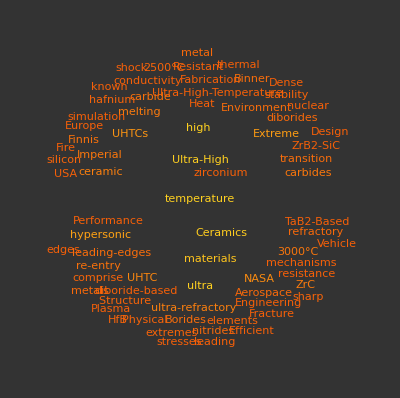

```mathematica
clouddy=WordCloud[data10,Disk[],ImageSize->400,Background->GrayLevel[0.2],ColorFunction->ColorData[{"SolarColors",{-0.5,0.5}}]]
```

```mathematica
Export["/Users/tom/scripts/XMat-slides/6-Nov-2017-note-revealJS/images/word-cloud-uhtc.png",clouddy]
```

/Users/tom/scripts/XMat-slides/6-Nov-2017-note-revealJS/images/word-cloud-uhtc.png

```mathematica
300-0.211311-0.1055 0.32208 0.464199 0.310099
760-0.359753 0.0516561 0.51115 1.63548 1.28142
1900 0.254366 0.479729 3.30569 7.12954 7.19955
2500-1.95415 2.65012 5.30936 8.39586 12.0715
3200-1.85128 1.87739 7.0026 12.7173 16.1709
3805-4.17644 0.296157 8.09224 14.0172 19.0386
```

```mathematica
meam={{1,2,3},{5,6,7},{10,11,12}}
```

{{1,2,3},{5,6,7},{10,11,12}}

```mathematica
dif=Transpose[Transpose[meam][[2;;3]]]-Transpose[Transpose[meam][[2;;3]]]^2
```

{{-2,-6},{-30,-42},{-110,-132}}

```mathematica
Norm[-2]
```

2

```mathematica
Sqrt[Mean[dif^2]]
Sqrt[Mean[Transpose@dif^2]]
Sqrt[Mean[Flatten[dif^2]]]
```

{2 √(3251/3),6 √178}

{2 √5,6 √37,11 √122}

```mathematica
Sqrt[Mean[Flatten[dif^2]]]
```

√(16114/3)

```mathematica
Table[Norm/@dif[[i]],{i,1,Length@dif}]
```

{{2,6},{30,42},{110,132}}